## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
Take[data,5]
```

{{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{area-of-circle,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,1},{bernoulli,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,0,1},{combo-magnification,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{compo-general-case,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

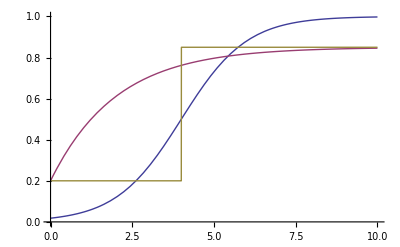

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Map[{#[[1]],Which[
(* too few data points *)
Length[Drop[#,3]]<Length[vars],Null,
(* These functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[Drop[#,3],0]==0 || Count[Drop[#,3],1]==0,2 Length[vars],True,Block[{x=NMaximize[{logProb[model,vars,Drop[#,3]],constraints[Drop[#,3]]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[#,x];False]]]}&,data]
```

```mathematica
data[[29]]
```

{define-image-distance,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,1,0,1}

```mathematica
logisticConstraints[x_]:=Block[{delta=12,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta && b<2 delta]
```

```mathematica
logisticConstraints[{0,0,1,1}]
```

mu≥-12+Max[b,2 b]&&mu≤12+Min[3 b,4 b]&&b>-24&&b<24

```mathematica
TableForm[maxer[logistic,{mu,b},logisticConstraints,Take[data,9]]]
```

NMaximize::nnum: The function value Experimental`NumericalFunction[{Hold[« 19 » + « 25 »], Block}, « 4 », {None, None, None}] is not a number at {b, mu} = {2.045600701889839`, -0.2952582547811935`}.

{compo-general-case,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1}{Log[1/(1+ⅇ^(-35 b+mu))]+Log[1/(1+ⅇ^(-34 b+mu))]+Log[1/(1+ⅇ^(-33 b+mu))]+Log[1/(1+ⅇ^(-32 b+mu))]+Log[1/(1+ⅇ^(-31 b+mu))]+Log[1/(1+ⅇ^(-30 b+mu))]+Log[1/(1+ⅇ^(-29 b+mu))]+Log[1/(1+ⅇ^(-28 b+mu))]+Log[1/(1+ⅇ^(-27 b+mu))]+Log[1/(1+ⅇ^(-26 b+mu))]+Log[1/(1+ⅇ^(-25 b+mu))]+Log[1/(1+ⅇ^(-22 b+mu))]+Log[1/(1+ⅇ^(-21 b+mu))]+Log[1/(1+ⅇ^(-20 b+mu))]+Log[1/(1+ⅇ^(-19 b+mu))]+Log[1/(1+ⅇ^(-18 b+mu))]+Log[1/(1+ⅇ^(-17 b+mu))]+Log[1/(1+ⅇ^(-16 b+mu))]+Log[1/(1+ⅇ^(-15 b+mu))]+Log[1/(1+ⅇ^(-14 b+mu))]+Log[1/(1+ⅇ^(-12 b+mu))]+Log[1/(1+ⅇ^(-11 b+mu))]+Log[1/(1+ⅇ^(-9 b+mu))]+Log[1/(1+ⅇ^(-8 b+mu))]+Log[1/(1+ⅇ^(-7 b+mu))]+Log[1/(1+ⅇ^(-6 b+mu))]+Log[1/(1+ⅇ^(-5 b+mu))]+Log[1/(1+ⅇ^(-4 b+mu))]+Log[1/(1+ⅇ^(-b+mu))]+Log[1-1/(1+ⅇ^(-24 b+mu))]+Log[1-1/(1+ⅇ^(-23 b+mu))]+Log[1-1/(1+ⅇ^(-13 b+mu))]+Log[1-1/(1+ⅇ^(-10 b+mu))]+Log[1-1/(1+ⅇ^(-3 b+mu))]+Log[1-1/(1+ⅇ^(-2 b+mu))],{b→2.0456,mu→-0.295258}}

NMaximize::nnum: The function value Experimental`NumericalFunction[{Hold[« 19 » + « 55 »], Block}, « 4 », {None, None, None}] is not a number at {b, mu} = {2.045600701889839`, -0.2952582547811935`}.

{compo-parallel-axis,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,1,1,1,1,0,0,1,1,1,1,1,1,0,1,0,1,1,1,0,0,1,0,1,0,1,1,1,1,1,0,1,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,1,1,0,1,1,1,1,1}{Log[1/(1+ⅇ^(-65 b+mu))]+Log[1/(1+ⅇ^(-64 b+mu))]+Log[1/(1+ⅇ^(-63 b+mu))]+Log[1/(1+ⅇ^(-62 b+mu))]+Log[1/(1+ⅇ^(-61 b+mu))]+Log[1/(1+ⅇ^(-59 b+mu))]+Log[1/(1+ⅇ^(-58 b+mu))]+Log[1/(1+ⅇ^(-55 b+mu))]+Log[1/(1+ⅇ^(-54 b+mu))]+Log[1/(1+ⅇ^(-53 b+mu))]+Log[1/(1+ⅇ^(-52 b+mu))]+Log[1/(1+ⅇ^(-51 b+mu))]+Log[1/(1+ⅇ^(-50 b+mu))]+Log[1/(1+ⅇ^(-47 b+mu))]+Log[1/(1+ⅇ^(-46 b+mu))]+Log[1/(1+ⅇ^(-45 b+mu))]+Log[1/(1+ⅇ^(-44 b+mu))]+Log[1/(1+ⅇ^(-43 b+mu))]+Log[1/(1+ⅇ^(-42 b+mu))]+Log[1/(1+ⅇ^(-41 b+mu))]+Log[1/(1+ⅇ^(-40 b+mu))]+Log[1/(1+ⅇ^(-34 b+mu))]+Log[1/(1+ⅇ^(-33 b+mu))]+Log[1/(1+ⅇ^(-32 b+mu))]+Log[1/(1+ⅇ^(-30 b+mu))]+Log[1/(1+ⅇ^(-29 b+mu))]+Log[1/(1+ⅇ^(-28 b+mu))]+Log[1/(1+ⅇ^(-27 b+mu))]+Log[1/(1+ⅇ^(-26 b+mu))]+Log[1/(1+ⅇ^(-24 b+mu))]+Log[1/(1+ⅇ^(-22 b+mu))]+Log[1/(1+ⅇ^(-19 b+mu))]+Log[1/(1+ⅇ^(-18 b+mu))]+Log[1/(1+ⅇ^(-17 b+mu))]+Log[1/(1+ⅇ^(-15 b+mu))]+Log[1/(1+ⅇ^(-13 b+mu))]+Log[1/(1+ⅇ^(-12 b+mu))]+Log[1/(1+ⅇ^(-11 b+mu))]+Log[1/(1+ⅇ^(-10 b+mu))]+Log[1/(1+ⅇ^(-9 b+mu))]+Log[1/(1+ⅇ^(-8 b+mu))]+Log[1/(1+ⅇ^(-5 b+mu))]+Log[1/(1+ⅇ^(-4 b+mu))]+Log[1/(1+ⅇ^(-3 b+mu))]+Log[1/(1+ⅇ^(-2 b+mu))]+Log[1-1/(1+ⅇ^(-60 b+mu))]+Log[1-1/(1+ⅇ^(-57 b+mu))]+Log[1-1/(1+ⅇ^(-56 b+mu))]+Log[1-1/(1+ⅇ^(-49 b+mu))]+Log[1-1/(1+ⅇ^(-48 b+mu))]+Log[1-1/(1+ⅇ^(-39 b+mu))]+Log[1-1/(1+ⅇ^(-38 b+mu))]+Log[1-1/(1+ⅇ^(-37 b+mu))]+Log[1-1/(1+ⅇ^(-36 b+mu))]+Log[1-1/(1+ⅇ^(-35 b+mu))]+Log[1-1/(1+ⅇ^(-31 b+mu))]+Log[1-1/(1+ⅇ^(-25 b+mu))]+Log[1-1/(1+ⅇ^(-23 b+mu))]+Log[1-1/(1+ⅇ^(-21 b+mu))]+Log[1-1/(1+ⅇ^(-20 b+mu))]+Log[1-1/(1+ⅇ^(-16 b+mu))]+Log[1-1/(1+ⅇ^(-14 b+mu))]+Log[1-1/(1+ⅇ^(-7 b+mu))]+Log[1-1/(1+ⅇ^(-6 b+mu))]+Log[1-1/(1+ⅇ^(-b+mu))],{b→2.0456,mu→-0.295258}}

NMaximize::nnum: The function value Experimental`NumericalFunction[{Hold[« 19 » + « 18 »], Block}, « 4 », {None, None, None}] is not a number at {b, mu} = {2.045600701889839`, -0.2952582547811935`}.

General::stop: Further output of NMaximize will be suppressed during this calculation.

{compo-perpendicular,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,1,1,0,0,0,1,1,1,1,0,1,1,0,0,1,0,0,1,1,1,0,0,0,1,1,1,1}{Log[1/(1+ⅇ^(-28 b+mu))]+Log[1/(1+ⅇ^(-27 b+mu))]+Log[1/(1+ⅇ^(-26 b+mu))]+Log[1/(1+ⅇ^(-25 b+mu))]+Log[1/(1+ⅇ^(-21 b+mu))]+Log[1/(1+ⅇ^(-20 b+mu))]+Log[1/(1+ⅇ^(-19 b+mu))]+Log[1/(1+ⅇ^(-16 b+mu))]+Log[1/(1+ⅇ^(-13 b+mu))]+Log[1/(1+ⅇ^(-12 b+mu))]+Log[1/(1+ⅇ^(-10 b+mu))]+Log[1/(1+ⅇ^(-9 b+mu))]+Log[1/(1+ⅇ^(-8 b+mu))]+Log[1/(1+ⅇ^(-7 b+mu))]+Log[1/(1+ⅇ^(-3 b+mu))]+Log[1/(1+ⅇ^(-2 b+mu))]+Log[1/(1+ⅇ^(-b+mu))]+Log[1-1/(1+ⅇ^(-24 b+mu))]+Log[1-1/(1+ⅇ^(-23 b+mu))]+Log[1-1/(1+ⅇ^(-22 b+mu))]+Log[1-1/(1+ⅇ^(-18 b+mu))]+Log[1-1/(1+ⅇ^(-17 b+mu))]+Log[1-1/(1+ⅇ^(-15 b+mu))]+Log[1-1/(1+ⅇ^(-14 b+mu))]+Log[1-1/(1+ⅇ^(-11 b+mu))]+Log[1-1/(1+ⅇ^(-6 b+mu))]+Log[1-1/(1+ⅇ^(-5 b+mu))]+Log[1-1/(1+ⅇ^(-4 b+mu))],{b→2.0456,mu→-0.295258}}

accel-constant-speed | Null
area-of-circle | 4.00002
bernoulli | 4.00002
combo-magnification | Null
compo-general-case | False
compo-general-case-unknown | Null
compo-parallel-axis | False
compo-perpendicular | False
compo-z-axis | 16.891

```mathematica
TableForm[maxer[logistic,{mu,b},logisticConstraints,data]]
```

accel-constant-speed | Null
area-of-circle | 4.00134
bernoulli | 4.00134
combo-magnification | Null
compo-general-case | 33.8361
compo-general-case-unknown | Null
compo-parallel-axis | False
compo-perpendicular | 41.5199
compo-z-axis | 16.891
compo-zero-vector | Null
continuity | 4.00134
define-angle-between-lines | 4
define-angular-frequency | 8.69497
define-area | Null
define-area-at | 4
define-charge | 29.0253
define-coef-friction | Null
define-compression | 4
define-current-thru | 17.6094
define-distance | 4.00134
define-distance-between | 10.5404
define-duration | 22.6107
define-electric-power-var | 4.00134
define-energy-var | Null
define-flux | 4.00134
define-focal-length | 4.00134
define-frequency | 22.5724
define-grav-accel | 4
define-image-distance | 8.22397
define-index-of-refraction | 4
define-magnification | 4.00134
define-mass | 18.2314
define-mass-density | 4.00134
define-moment-of-inertia | 4.00134
define-object-distance | 4.00134
define-period-var | 8.22397
define-pressure | 15.8216
define-radius-of-circle | 4.00134
define-resistance-var | 15.5238
define-revolution-radius | 4
define-shape-length | 4.00134
define-slit-separation | 4.00134
define-speed | 8.33081
define-spring-constant | 7.81909
define-stored-energy-var | 4
define-turns | 4
define-voltage-across | 23.6526
define-volume | Null
define-wavelength | 4.00134
define-work | 7.81909
definition-syntax | 4
draw-accel-free-fall | 4
draw-accel-slow-down | Null
draw-accel-speed-up | 14.7537
draw-ang-accel | Null
draw-ang-accel-speed-up | 4.00134
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 4
draw-ang-velocity-rotating | 4.00134
draw-applied-force | 4.00134
draw-bfield-straight-current | 8.22397
draw-bforce-charge | 4.00134
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | False
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.22397
draw-compo-form-axes | 17.9209
draw-coulomb-force-unknown | 4.00134
draw-displacement-given-dir | 8.33081
draw-displacement-straight | 10.3024
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 4.00134
draw-field-given-dir | 9.30275
draw-field-unknown | Null
draw-grav-force | 4
draw-impulse-given-momenta | Null
draw-kinetic-friction | 4
draw-line-given-dir | 14.7039
draw-line-unknown-dir | 4
draw-momentum-at-rest | 4
draw-momentum-straight | 12.8695
draw-net-field-given-dir | 4
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | 4.00134
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.7728
draw-point-efield-unknown | 4.00134
draw-projection-axes | 4
draw-relative-position | 8.36664
draw-relative-position-unknown | 4.00134
draw-spring-force | 4.00134
draw-tension | 15.8515
draw-torque | Null
draw-unrotated-axes | 27.0241
draw-vector-aligned-axes | 4
draw-velocity-at-rest | 9.54518
draw-velocity-curved | 15.1537
draw-velocity-curved-unknown | 4
draw-velocity-momentarily-at-rest | 10.9233
draw-velocity-straight | False
draw-velocity-straight-unknown | Null
draw-weight | 18.5417
draw-xy-vector-given-compos | 4.00134
draw-z-axis-vector-given-compos | 4.00134
equation-syntax | False
equiv-resistance-parallel | 9.54518
equiv-resistance-series | 4
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 8.69497
magnification-eqn | 4
object-label | 4
pendulum-oscillation | 4.00134
pressure-at-open-to-atmosphere | 4.00134
pressure-force | 4.00134
pressure-height-fluid | Null
sdd-constvel-compo | 9.54518
select-mc-answer | False
spring-law-compression | 4.00134
spring-mass-oscillation | Null
write-ang-momentum | 4.00134
write-angle-direction-known-lines | 4.00134
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | 4
write-capacitance-definition | 4.00134
write-centripetal-accel | 4.00134
write-change-me | Null
write-charge-force-bfield | 7.81909
write-charge-force-bfield-mag | 4.00134
write-charge-force-efield-compo | 4
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | 4.00134
write-cons-angmom | Null
write-cons-linmom-compo-join-split | 4
write-coulomb | Null
write-coulomb-compo | 4.00134
write-density | Null
write-electric-power | 8.22397
write-energy-cons | 4
write-equality | 4
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 4
write-g-on-earth | Null
write-grav-energy | 9.0061
write-harmonic-of | 4
write-height-dy | 4.00134
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 16.3653
write-known-value-eqn | False
write-linear-vel | Null
write-lk-no-s-compo | 14.3543
write-lk-no-t-compo | 4.00134
write-lk-no-vf-compo | 10.3024
write-loop-rule-capacitors | 12.4747
write-loop-rule-resistors | 10.7301
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 4.00134
write-net-field-compo | 4
write-net-force-compo | 10.5404
write-nfl-compo | 13.4378
write-nsl-compo | 21.9682
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 16.7064
write-period-circular | Null
write-point-charge-efield-compo | 4.00134
write-potential-energy | Null
write-right-triangle-tangent | 4.00134
write-rk-no-s | 4
write-rk-no-vf | Null
write-sdd | 8.22397
write-single-loop-rule | Null
write-slit-interference | 4.00134
write-snells-law | Null
write-spring-energy | 8.22397
write-straight-wire-bfield | 4.00134
write-sum-disp-compo | 4
write-sum-times | 4.00134
write-tensions-equal | 4
write-total-energy-top | 15.0904
write-transformer-power | Null
write-turns-per-length | Null
write-ug | 4.00134
write-unit-vector-mag | Null
write-vector-magnitude | 4.00134
write-wave-speed-light | Null
write-wnc | Null
write-work | 4.00134
wt-law | 16.6067

```mathematica
TableForm[maxer[bkt,{b,pg,ps},pg≥0 && ps≥0 && pg≤1 && ps≤ 1 &&b≥0,Take[data,20]]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6
combo-magnification | Null
compo-general-case | 35.8378
compo-general-case-unknown | Null
compo-parallel-axis | 85.444
compo-perpendicular | 42.5766
compo-z-axis | 18.3684
compo-zero-vector | Null

```mathematica
TableForm[maxer[step,{nl,pg,ps},pg≥0 && ps≥0 && pg≤1 && ps≤1 &&Element[nl,Integers]&&nl≥0,Take[data,20]]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6
combo-magnification | Null
compo-general-case | 34.6219
compo-general-case-unknown | Null
compo-parallel-axis | 84.7132
compo-perpendicular | 40.7894
compo-z-axis | 16.9895
compo-zero-vector | Null